```mathematica
(*Plot[{Sin[x],Cos[x]},{x,0,2π}]*)
```

```mathematica
(*s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}];Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]*)
```

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}];
Plot3D[Evaluate[u[t,x]/.%],{t,0,10},{x,0,5},PlotRange->All]
```

-Graphics3D-

## 问题 1

以下为问题 1(1) 参数。

```mathematica
m=2433;k2=80000;c2=10000;
f=6250;omega=1.4005;k1=1025*9.8*Pi;
c1=656.3616;m0=1335.535;M=4866;
```

100

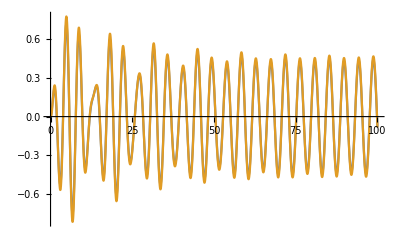

```mathematica
stop=100
s=NDSolve[{m*x2''[t]==k2(x1[t]-x2[t])+c2(x1'[t]-x2'[t]),f*Cos[omega*t]==k2(x1[t]-x2[t])+c2(x1'[t]-x2'[t])+k1*x1[t]+c1*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop}]
```

求得对应位移和速度为：

```mathematica
targets={10,20,40,60,100};
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
```

10 | -0.190711 | -0.641009 | -0.211679 | -0.693954
20 | -0.590684 | -0.240952 | -0.634248 | -0.272776
40 | 0.285375 | 0.312971 | 0.296499 | 0.332912
60 | -0.314505 | -0.479456 | -0.331435 | -0.515729
100 | -0.083614 | -0.604211 | -0.0840672 | -0.643002

修改为问题 1(2) 参数，重新计算。

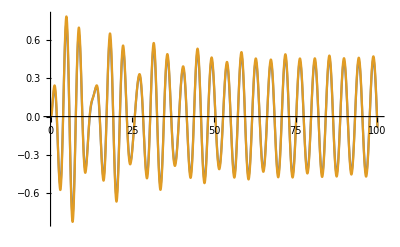

10 | -0.191991 | -0.644618 | -0.213781 | -0.701741
20 | -0.59419 | -0.245594 | -0.640176 | -0.28171
40 | 0.282215 | 0.306276 | 0.294026 | 0.325993
60 | -0.317233 | -0.482805 | -0.335615 | -0.520822
100 | -0.0848249 | -0.605817 | -0.0862467 | -0.645578

```mathematica
cv2[v_]:=10000*Sqrt[Abs[v]]
s=NDSolve[{m*x2''[t]==k2(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k2(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t])+k1*x1[t]+c1*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop}]
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
```

## 问题 2

以下为问题 2(1) 参数。

```mathematica
M=4866;m=2433;k2=80000;c2=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c1=167.8395;m0=1165.992;
```

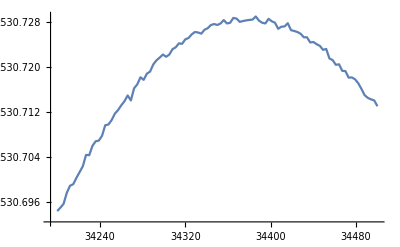

```mathematica
start=510;stop=520;dim=1;
P2[cm2_]:=Sum[cm2*((x1'[i]-x2'[i])^2)*dim,{i,start,stop,dim}]/.NDSolve[{m*x2''[t]==k2*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t]),f*Cos[omega*t]==k2*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t])+k1*x1[t]+c1*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
DrawP2[pStart_,pStop_,pStepNum_]:=ListLinePlot[Table[{i,First[P2[i]]},{i,Range[pStart,pStop,(pStop-pStart)/pStepNum]}]]
DrawP2[34200,34500,100]
```

```mathematica
cmv2[v_,ck_,ce_]:=ck*Abs[v]^ce;
P22I[ck_,ce_]:=NDSolve[{m*x2''[t]==k2*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k2*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t])+k1*x1[t]+c1*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
P22[ck_,ce_]:=Sum[cmv2[x1'[i]-x2'[i],ck,ce+2]*dim,{i,start,stop,dim}]/.P22I[ck,ce]
CalcP22[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Table[{k,e,First[P22[k,e]]},{k,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{e,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]
DrawP22[data_]:=ListPlot3D[Flatten[data,1]]
(*DrawP22[0,10000,10,0,1,10]*)
CalcP22[0,100000,8,0,1,8]
(*DrawP22[34200,34500,100]*)
(*First[P22[2,2]]*)
```

{{{0,0,0},{0,1/8,0},{0,1/4,0},{0,3/8,0},{0,1/2,0},{0,5/8,0},{0,3/4,0},{0,7/8,0},{0,1,0}},{{12500,0,1623.99},{12500,1/8,1307.17},{12500,1/4,1035.36},{12500,3/8,811.778},{12500,1/2,632.451},{12500,5/8,490.881},{12500,3/4,380.254},{12500,7/8,294.401},{12500,1,228.11}},{{25000,0,2406.96},{25000,1/8,2140.66},{25000,1/4,1816.05},{25000,3/8,1491.34},{25000,1/2,1197.7},{25000,5/8,947.916},{25000,3/4,743.112},{25000,7/8,579.045},{25000,1,449.585}},{{37500,0,2521.14},{37500,1/8,2483.19},{37500,1/4,2276.7},{37500,3/8,1979.37},{37500,1/2,1657.05},{37500,5/8,1349.13},{37500,3/4,1077.74},{37500,7/8,850.132},{37500,1,665.082}},{{50000,0,2362.03},{50000,1/8,2528.71},{50000,1/4,2486.68},{50000,3/8,2288.55},{50000,1/2,1999.68},{50000,5/8,1682.47},{50000,3/4,1375.55},{50000,7/8,1102.08},{50000,1,871.109}},{{62500,0,2135.42},{62500,1/8,2438.74},{62500,1/4,2539.64},{62500,3/8,2457.79},{62500,1/2,2240.38},{62500,5/8,1946.44},{62500,3/4,1632.14},{62500,7/8,1331.46},{62500,1,1065.3}},{{75000,0,1914.64},{75000,1/8,2298.76},{75000,1/4,2507.44},{75000,3/8,2531.02},{75000,1/2,2396.64},{75000,5/8,2149.55},{75000,3/4,1846.94},{75000,7/8,1536.28},{75000,1,1246.07}},{{87500,0,1719.83},{87500,1/8,2147.2},{87500,1/4,2433.45},{87500,3/8,2543.59},{87500,1/2,2488.56},{87500,5/8,2300.15},{87500,3/4,2024.07},{87500,7/8,1715.81},{87500,1,1412.39}},{{100000,0,1553.23},{100000,1/8,2000.88},{100000,1/4,2339.96},{100000,3/8,2519.79},{100000,1/2,2534.93},{100000,5/8,2405.88},{100000,3/4,2167.93},{100000,7/8,1871.49},{100000,1,1563.7}}}

```mathematica
s=%
```

{{{0,0,0},{0,1/8,0},{0,1/4,0},{0,3/8,0},{0,1/2,0},{0,5/8,0},{0,3/4,0},{0,7/8,0},{0,1,0}},{{12500,0,1623.99},{12500,1/8,1307.17},{12500,1/4,1035.36},{12500,3/8,811.778},{12500,1/2,632.451},{12500,5/8,490.881},{12500,3/4,380.254},{12500,7/8,294.401},{12500,1,228.11}},{{25000,0,2406.96},{25000,1/8,2140.66},{25000,1/4,1816.05},{25000,3/8,1491.34},{25000,1/2,1197.7},{25000,5/8,947.916},{25000,3/4,743.112},{25000,7/8,579.045},{25000,1,449.585}},{{37500,0,2521.14},{37500,1/8,2483.19},{37500,1/4,2276.7},{37500,3/8,1979.37},{37500,1/2,1657.05},{37500,5/8,1349.13},{37500,3/4,1077.74},{37500,7/8,850.132},{37500,1,665.082}},{{50000,0,2362.03},{50000,1/8,2528.71},{50000,1/4,2486.68},{50000,3/8,2288.55},{50000,1/2,1999.68},{50000,5/8,1682.47},{50000,3/4,1375.55},{50000,7/8,1102.08},{50000,1,871.109}},{{62500,0,2135.42},{62500,1/8,2438.74},{62500,1/4,2539.64},{62500,3/8,2457.79},{62500,1/2,2240.38},{62500,5/8,1946.44},{62500,3/4,1632.14},{62500,7/8,1331.46},{62500,1,1065.3}},{{75000,0,1914.64},{75000,1/8,2298.76},{75000,1/4,2507.44},{75000,3/8,2531.02},{75000,1/2,2396.64},{75000,5/8,2149.55},{75000,3/4,1846.94},{75000,7/8,1536.28},{75000,1,1246.07}},{{87500,0,1719.83},{87500,1/8,2147.2},{87500,1/4,2433.45},{87500,3/8,2543.59},{87500,1/2,2488.56},{87500,5/8,2300.15},{87500,3/4,2024.07},{87500,7/8,1715.81},{87500,1,1412.39}},{{100000,0,1553.23},{100000,1/8,2000.88},{100000,1/4,2339.96},{100000,3/8,2519.79},{100000,1/2,2534.93},{100000,5/8,2405.88},{100000,3/4,2167.93},{100000,7/8,1871.49},{100000,1,1563.7}}}

{0.,0.,0.} | {0.,0.125,0.} | {0.,0.25,0.} | {0.,0.375,0.} | {0.,0.5,0.} | {0.,0.625,0.} | {0.,0.75,0.} | {0.,0.875,0.} | {0.,1.,0.}
{12500.,0.,1623.99} | {12500.,0.125,1307.17} | {12500.,0.25,1035.36} | {12500.,0.375,811.778} | {12500.,0.5,632.451} | {12500.,0.625,490.881} | {12500.,0.75,380.254} | {12500.,0.875,294.401} | {12500.,1.,228.11}
{25000.,0.,2406.96} | {25000.,0.125,2140.66} | {25000.,0.25,1816.05} | {25000.,0.375,1491.34} | {25000.,0.5,1197.7} | {25000.,0.625,947.916} | {25000.,0.75,743.112} | {25000.,0.875,579.045} | {25000.,1.,449.585}
{37500.,0.,2521.14} | {37500.,0.125,2483.19} | {37500.,0.25,2276.7} | {37500.,0.375,1979.37} | {37500.,0.5,1657.05} | {37500.,0.625,1349.13} | {37500.,0.75,1077.74} | {37500.,0.875,850.132} | {37500.,1.,665.082}
{50000.,0.,2362.03} | {50000.,0.125,2528.71} | {50000.,0.25,2486.68} | {50000.,0.375,2288.55} | {50000.,0.5,1999.68} | {50000.,0.625,1682.47} | {50000.,0.75,1375.55} | {50000.,0.875,1102.08} | {50000.,1.,871.109}
{62500.,0.,2135.42} | {62500.,0.125,2438.74} | {62500.,0.25,2539.64} | {62500.,0.375,2457.79} | {62500.,0.5,2240.38} | {62500.,0.625,1946.44} | {62500.,0.75,1632.14} | {62500.,0.875,1331.46} | {62500.,1.,1065.3}
{75000.,0.,1914.64} | {75000.,0.125,2298.76} | {75000.,0.25,2507.44} | {75000.,0.375,2531.02} | {75000.,0.5,2396.64} | {75000.,0.625,2149.55} | {75000.,0.75,1846.94} | {75000.,0.875,1536.28} | {75000.,1.,1246.07}
{87500.,0.,1719.83} | {87500.,0.125,2147.2} | {87500.,0.25,2433.45} | {87500.,0.375,2543.59} | {87500.,0.5,2488.56} | {87500.,0.625,2300.15} | {87500.,0.75,2024.07} | {87500.,0.875,1715.81} | {87500.,1.,1412.39}
{100000.,0.,1553.23} | {100000.,0.125,2000.88} | {100000.,0.25,2339.96} | {100000.,0.375,2519.79} | {100000.,0.5,2534.93} | {100000.,0.625,2405.88} | {100000.,0.75,2167.93} | {100000.,0.875,1871.49} | {100000.,1.,1563.7}

-Graphics3D-

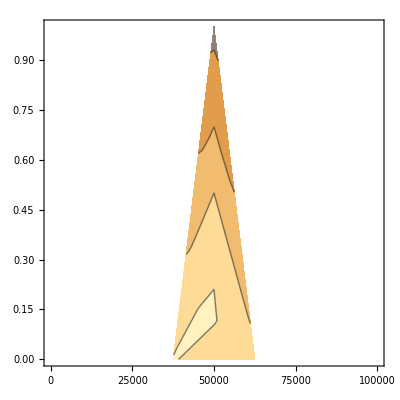

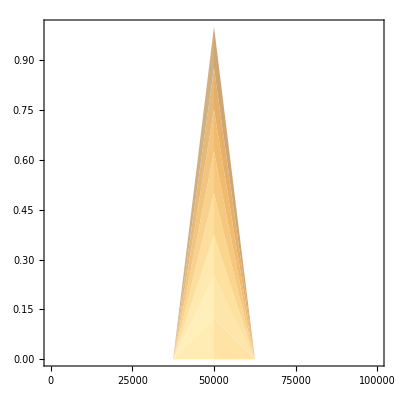

```mathematica
Grid[N[s]]
ListPlot3D[Flatten[s,1]]
ListContourPlot[Flatten[s,1]]
ListDensityPlot[Flatten[s,1]]
```

## 问题 3

```mathematica
Clear["Global`*"];
d=1;
l0=1;
m=1;
k=1;
c=1;
g=9.8;
kr=1;
cr=1;
Ib=1;
Ia=1;
Fw=1;
M=1;
Fx=1;
xg=0;
Mf=1;
L=1;
w=1;
f=1;

Fw:=f*Cos[w*t];
Fx:=1*Abs[zg'[t]];
Mx[t_]:=1*Abs[th'[t]];
Mj[t_]:=1*Abs[th[t]];
Mw[t_]:=L*Cos[o*t];
za[t_]:=zg[t]-d*Cos[th[t]];
th2[t_]:=th[t]+ga[t];
xp[t_]:=xg-d*Sin[th[t]]+l[t]*Sin[th2[t]];
zp[t_]:=(-d)*Cos[th[t]]+l[t]*Cos[th2[t]];
F[t_]:=k*(l[t]-l0)+c*l'[t];
Mab[t_]:=kr*ga[t]+cr*ga'[t];
NDSolve[{m*xp''[t]==F[t]*Sin[th2[t]],m*zp''[t]==F[t]*Cos[th2[t]]-m*g,Ib*th2''[t]==Mab[t]+F[t]*l[t],Fw[t]-M*g-F[t]*Cos[th2[t]]-Fx-Ff==M*zg''[t],(*Ia*th''[t]==-Mab[t]+F[t]*d+Mw[t]-Mx[t]-Mf-Mj[t],*)(*l[t]==l0-1/k*(m*g+c/Cos[th2[t]]*(zp[t]-za[t])),*)th[0]==th'[0]==ga[0]==ga'[0]==l[0]==l'[0]==zg[0]==zg'[0]==0},{th,ga,zg,l},{t,0,100}]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

$Failed

NDSolve[{Sin[th[t]] th'[t]^2+2 Cos[ga[t]+th[t]] l'[t] (ga'[t]+th'[t])-l[t] Sin[ga[t]+th[t]] (ga'[t]+th'[t])^2+Sin[ga[t]+th[t]] l''[t]-Cos[th[t]] th''[t]+Cos[ga[t]+th[t]] l[t] (ga''[t]+th''[t])==Sin[ga[t]+th[t]] (-1+l[t]+l'[t]),Cos[th[t]] th'[t]^2-2 Sin[ga[t]+th[t]] l'[t] (ga'[t]+th'[t])-Cos[ga[t]+th[t]] l[t] (ga'[t]+th'[t])^2+Cos[ga[t]+th[t]] l''[t]+Sin[th[t]] th''[t]-l[t] Sin[ga[t]+th[t]] (ga''[t]+th''[t])==-9.8+Cos[ga[t]+th[t]] (-1+l[t]+l'[t]),ga''[t]+th''[t]==ga[t]+ga'[t]+l[t] (-1+l[t]+l'[t]),-9.8-Ff-Abs[zg'[t]]+Cos[t][t]-Cos[ga[t]+th[t]] (-1+l[t]+l'[t])==zg''[t],th[0]==th'[0]==ga[0]==ga'[0]==l[0]==l'[0]==zg[0]==zg'[0]==0},{th,ga,zg,l},{t,0,100}]